# Mathematica Shortcuts

Math 250 - Mathematical Computing
Christopher Hanusa

## 4.1 Aim

This tutorial is about some best practices for Mathematica, and some shortcuts to make your life with Mathematica easier.

## 4.2 NOT losing your work

### Save your work

Mathematica is more likely to crash than other programs you’re used to, especially when you’re in the middle of a complex computation, or when it is right before your project is due.  Save your notebooks frequently.

### AutoSave!

It is possible to turn on the AutoSave feature of Mathematica.  What it will do is save your work every time you do an evaluation. (Shift-Return)  Follow these steps to turn it on:

Go to Preferences > Advanced

Click on “Open Option Inspector”

Ensure that “Global Preferences” is selected in the “Scope” pulldown menu.

In the Search Bar type in AutoSave

Click the checkbox next to “NotebookAutoSave”.

The only problem I have found with enabling AutoSave is that it slows down your coding process because it makes the computer work more often.  The piece of mind you get from knowing that your work is being saved regularly is worth it.  If things really start to go very slowly, it’s probably because your notebook is very very large.  When this happens to me, I save my work, I open a new notebook and bring over the most essential pieces of code into the new notebook and work from there.

### Undo

Mathematica has an undo command (Ctrl-Z or Option-Z is the keyboard shortcut). BUT it doesn’t always work, and don’t depend on it being able to undo more than one thing.

### Incremental Development

One way to avoid using an Undo command and that is a good programming practice that you should start to use is incremental development.  It boils down to three principles:

Always start with a piece of working code.

Make only one small modification at a time.

Test the new code to see if the change worked.

This is helpful because if you change something small and it breaks, it’s easy to find.  On the other hand, if you try to write a piece of code that is complex all in one go, then if it doesn’t work it will be much harder to find your error.

In a Mathematica notebook, the best way to do this is to start with a “Minimal Working Example”, such as a piece of code from the Documentation Center.  Then as you build your code and it becomes more and more complex:

Copy a piece of code that is working the way you want it to into a new cell just underneath.

Modify the code in the new cell in a new way.

Run the code in the new cell to see if it does what you want it to.  If so, repeat the cycle.  If not, check to see where it went wrong.

Example. Join a string with its reversal.

## Draft

```mathematica
"abcd"<>"ABCD"<>"xyz"
```

abcdABCDxyz

```mathematica
Reverse["abcd"]
```

Reverse::normal: Nonatomic expression expected at position 1 in Reverse[abcd].

Reverse[abcd]

```mathematica
StringReverse["abcdef"]
```

fedcba

## This one works!

```mathematica
"abcd"<>"ABCD"<>"xyz"
```

abcdABCDxyz

```mathematica
StringReverse["abcdef"]
```

fedcba

```mathematica
"abc"<>StringReverse["abc"]
```

abccba

## Back to the future

### Cloud Storage

It is good practice to save your work in multiple places so that you won’t lose your work if your computer dies.  One good way to do this is to use cloud storage.  Three good versions are Dropbox (available for CUNY), Google Drive (available as part of the QC Google Apps for Education), and Microsoft OneDrive (available as part of your QMail account).  You should create an account on one of these services and make sure to upload your files to them.  In this way you will have access to them anywhere there is internet. You can also save them in the Wolfram Cloud, but I wouldn’t consider that as reliable of an option.  If you have questions about this see me.

## 4.3 Defining variables using the = operator

It is often helpful to define the output of a command to be able to reuse it later.  To do this, use the = operator:

```mathematica
a=Range[3]
```

{1,2,3}

```mathematica
a
```

{1,2,3}

If you don’t want to see the output of a command, you can end the line with a semicolon.

```mathematica
a=Range[4];
```

```mathematica
a
```

{1,2,3}

Important: it matters the order in which you evaluate commands.  For example, if you re-evaluate the first instance of a, it will return its last-defined definition, which is {1,2,3,4}.

I HIGHLY suggest that you give descriptive names to your variables. Since all built-in Mathematica commands start with a capital letter, a nice convention to use for your own variable names is to start with a lowercase letter and if variable is multiple words long, capitalize the start of each new word.

```mathematica
iAmANewVariable=Range[Pi,2Pi,Pi/2]
```

{π,(3 π)/2,2 π}

```mathematica
heyYouWhatsThatSound=Play[Sin[440 2Pi t],{t,0,1}]
```

-Graphics-

(OK, the provided example names aren’t very descriptive, but you get the idea....it’s #likeAHashtag.)

## 4.4 Shortcut: the % operator

A useful but slightly dangerous operator is %, which stands for the most recent output.  So, for instance, if you decide to make a list, and then decide you want to create a scatterplot, you can do the following:

```mathematica
ourIntegers=Table[RandomInteger[{1,3}],{100}]
```

{3,2,3,1,3,1,3,2,1,2,3,1,1,3,3,3,3,2,1,2,1,3,2,2,2,2,3,2,3,2,2,2,1,3,3,2,1,1,1,2,3,1,2,1,3,2,1,2,3,2,2,1,1,3,1,2,2,3,2,3,3,3,2,3,3,3,2,1,3,3,1,1,1,1,3,3,2,1,1,3,2,1,2,1,1,2,3,3,1,1,1,2,2,1,2,2,2,3,3,1}

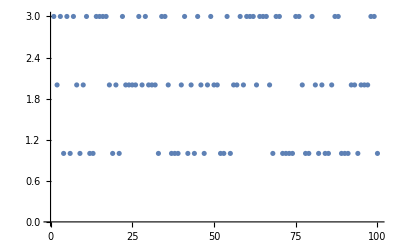

```mathematica
ListPlot[ourIntegers]
```

The reason it is dangerous is related to the above discussion where the order in which you evaluate commands matters.  If you tried to re-evaluate the previous line of code, you would get an error, because you can’t create a scatterplot of a scatterplot!

```mathematica
ListPlot[ourIntegers]
```

-Graphics-

In the same vein is %% (for two outputs back); slightly more safe might be Out[n] to be explicit about wanting the nth output.  (But this will depend on the session in which you are working, so it would be different each time you re-open your notebook!!!!)  It is best to define a new variable when you think you will be using the output later.

## 4.5 When you’ve gotten yourself in trouble

### When you don’t understand a command.

By now you should know that you can search in the Documentation Center when you want more information about a command.  You can also get quick information about a command directly in a Mathematica notebook by using the ? operator.

```mathematica
?Tally
```

Tally[list] tallies the elements in list, listing all distinct elements together with their multiplicities.
Tally[list,test] uses test to determine whether pairs of elements should be considered equivalent, and gives a list of the first representatives of each equivalence class, together with their multiplicities.

Notice the >> symbol at the end of the command information.  Click there to go directly to the Documentation Center.

You can also hover over a command to open up this quick command information or to go directly to the Documentation Center.

### When you define something you shouldn’t have.

Suppose you define a variable at some point:

```mathematica
x=10
```

10



```mathematica
x=Graphics[RegularPolygon[4]]
```

Perhaps later in your file you wanted to generate the list {x+1,x+2,x+3} using the Table command:

```mathematica
Table[x+i,{i,3}]
```

{1+-Graphics-,2+-Graphics-,3+-Graphics-}

Since x had been defined before, the generated list has no x’s in it.  When you run into such a problem, you use the Remove command:

```mathematica
Remove[x];
Table[x+i,{i,3}]
```

{1+x,2+x,3+x}

### When your code won’t stop running

We all get into infinite loops sometimes.  To stop Mathematica in the middle of a calculation, use (Option-.) or (Alt-.)  (That’s the period!)  
Try it here after removing the (* and *) which I used to comment out the command.

```mathematica
For[i=0,i≥0,i++,i]
```

$Aborted

## 4.7 Shorthand: @ (Prefix)

When your function takes only one input, you can use the @ symbol as a shortcut in lieu of the square brackets.

```mathematica
Length[{1,2,3,4}]
```

4

For example, we can rewrite the above code as:

```mathematica
Length@{1,2,3,4}
```

4

```mathematica
Range[4]
```

{1,2,3,4}

```mathematica
Length@%
```

4

You CANNOT use the @ symbol when your function has multiple inputs. (Like Table)

Key points:

You do not have to use the @ symbol.

It is important to be aware of the @ symbol because it will appear in code you find online.

You should first work to be comfortable using functions with bracket notation and eventually you may find it useful.